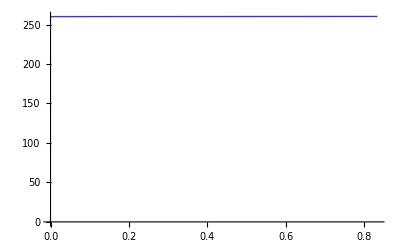

```mathematica
f[x_]:=0.25x+260
p=Plot[{f[x]},{x,0,5/6},AxesOrigin->{0,0}]
```

```mathematica
460/800//N
```

0.575

```mathematica
Export["ex14.pdf",p,"PDF"]
```

ex14.pdf

ex07.pdf

```mathematica
Export["ex05b.pdf",%15,"PDF"]
```

ex05b.pdf

```mathematica
LinearSolve[{{4,-2,1},{0,0,1},{1,1,1}},{2,1,-2.5}]
```

{-1.,-2.5,1.}

```mathematica
T[t_]:=.02t+8.5
```

```mathematica
T[2100-1900]
```

12.5

```mathematica
c[a_]:=(.0417*200)(a+1)
```

```mathematica
Expand[c[a]]
```

8.34+8.34 a

```mathematica
4/5 60
```

48

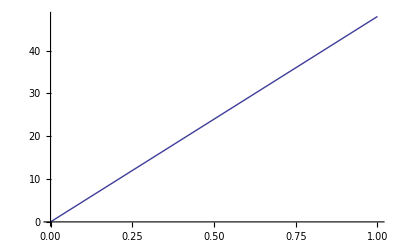

```mathematica
Plot[48x,{x,0,1}]
```

```mathematica
(4800-2200)/200
```

13

```mathematica
Reduce[2200==1300+b,b]
```

b==900

```mathematica
m[x_,y_]:=(250-y)/(15-x)//N
```

```mathematica
m[{5,10,20,25,30},{694,444,111,28,0}]//Round//Mean
```

-30

```mathematica
ListPlot[Table[{5,10,15,20,25,30},{694,444,250,111,28,0}]]
```

Table::itform: Argument {694, 444, 250, 111, 28, 0} at position 2 does not have the correct form for an iterator.

ListPlot::lpn: Table[{5, 10, 15, 20, 25, 30}, {694, 444, 250, 111, 28, 0}] is not a list of numbers or pairs of numbers.

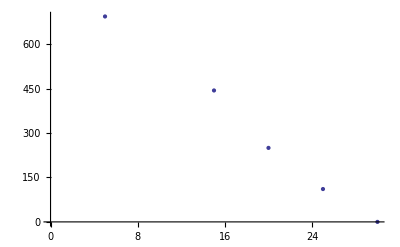

```mathematica
ListPlot[{{5,694},{15,444},{20,250},{25,111},{30,0}}]
```

```mathematica
Export["ex01.pdf",%30]
```

ex01.pdf

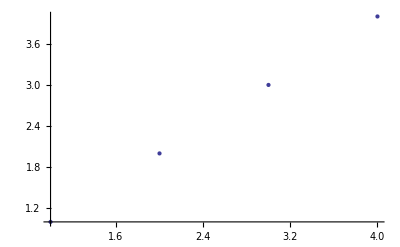

```mathematica
ListPlot[{1,2,3,4},]
```

```mathematica
[]
```

/Users/edwint/Documents/U/ubb/sccc/calculus/week02/hw/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/edwint/Documents/U/ubb/sccc/calculus/week02/hw

```mathematica
ex02[x_,y_]:=(y-2948)/(x-42)//N
```

```mathematica
ex02[{36,38,40,44},{2530,2661,2806,3080}]//Round
```

{70,72,71,66}

```mathematica
secant[f,x1_,x2_]:=(f[x2]-f[x1])/(x2-x1)
```

```mathematica
f[x_]:=x/(1+x)
```

```mathematica
secant[f,1,0.99]
```

0.251256

```mathematica
LinearSolve[{{480,1},{800,1}},{380,460}]//N
```

{0.25,260.}